```mathematica
SetDirectory["C:\\Users\\pglpm\\repositories\\maxNt\\scripts\\"];
```

```mathematica
(* Study of maxent at the "sample" or "population" level. Stensola data *)
```

```mathematica
(* assumptions *)
assu=(Element[nn||rr||n||r||m,Integers]&&nn≥n≥1&&0≤rr≤nn&&0≤r≤n&&0≤m≤n&&0<k<1&&0<a<1&&0<aa<1&&nn*aa≥n*a&&aa≥k*a);
```

```mathematica
(* hypergeometric distribution for sample given population *)

Clear[condp2];condp2[n_,a_,nn_,aa_]:=(N@Binomial[n,a]*N@Binomial[nn-n,aa-a]/N@Binomial[nn,aa])
```

```mathematica
Clear[condp];condp[n_,a_,nn_,aa_]:=(Binomial[n,a]*Binomial[nn-n,aa-a]/Binomial[nn,aa]//N)
```

```mathematica
(* load values already calculated of the hypergeometric distribution *)
Import[$HomeDirectory<>"\\work\\largefiles\\condp.zip","*"];
```

$Aborted

```mathematica
(* save values already calculated of the hypergeometric distribution *)Save["condp.m",condp]
```

```mathematica
(* Define various symbols to be used in plots *)

sidesquare=2*Sqrt[3]*3/8;
radiuscircle=Sqrt[(2*Sqrt[3]*3/2)/Pi];
(*radiuscircle=2*Sqrt[3]*3/(2*Pi);*)

size=2;absoluteThickness=1;
emptySquare=Graphics[{AbsoluteThickness[absoluteThickness],JoinedCurve[Line[{Offset[size {sidesquare,sidesquare}],Offset[size {-sidesquare,sidesquare}],Offset[size {-sidesquare,-sidesquare}],Offset[size {sidesquare,-sidesquare}]}],CurveClosed->True]},AlignmentPoint->{0,0}];
emptyUpTriangle=Graphics[{AbsoluteThickness[absoluteThickness],JoinedCurve[Line[{Offset[size {0,2}],Offset[size {Sqrt[3],-1}],Offset[size {-Sqrt[3],-1}]}],CurveClosed->True]},AlignmentPoint->{0,0}];
filledUpTriangle=Graphics[{Triangle[{Offset[size {0,2}+absoluteThickness {0,1}],Offset[size {Sqrt[3],-1}+absoluteThickness {Sqrt[3/4],-1/2}],Offset[size {-Sqrt[3],-1}+absoluteThickness {-Sqrt[3/4],-1/2}]}]},AlignmentPoint->{0,0}];
{emptyLeftTriangle,filledLeftTriangle,emptyDownTriangle,filledDownTriangle,emptyRightTriangle,filledRightTriangle}=Flatten[{emptyUpTriangle,filledUpTriangle}/.{x_?NumericQ,y_?NumericQ}:>RotationTransform[#][{x,y}]&/@{Pi/2,Pi/3,-Pi/2}];
emptyCircle=Graphics[{AbsoluteThickness[absoluteThickness],Circle[{0,0},Offset[size*radiuscircle+absoluteThickness]]},AlignmentPoint->{0,0}];
```

```mathematica
(* load scripts to calculate the Lagrange multipliers from the constraints *)
<<"ME_homsolution.m";<<"ME_homsolution2.m";
```

```mathematica
MEhomprob[js1_,js2_,nn_]:=Block[{prob},prob=Table[Binomial[nn,m]*Exp[js2*(m^2-m)/(nn^2-nn)+js1*m/nn],{m,0,nn}];
prob/Total[prob]];
```

```mathematica
(* load first four raw moments from Stensola data (3 ms) *)

n=65;means=Flatten@Import["norm_binomeans.csv"][[2;;]]
```

{0.0124204,0.000216286,4.59777×10^-6,1.07013×10^-7}

```mathematica
{aa1,aa2,aa3,aa4}=means;
```

```mathematica
nn=5000;rann=Range[0,nn];
```

```mathematica
(* find Lagr multipliers, 2 constraints.
MEhomsolution usually give better-precision results than MEhomsolution2 *)
{zj1,zj2,qpop,norm2}=MEhomsolution[aa1,aa2,nn,12];
```

```mathematica
{zj1,zj2}
```

{-22460.8632984,22450.9645408}

```mathematica
(* find Lagr multipliers, 2 constraints *)
{zj1,zj2,qq2ex,norm2}=MEhomsolution2[aa1,aa2,nn,12];
```

```mathematica
{zj1,zj2}
```

{-22449.2940092,22429.6391226}

```mathematica
{{"measured",aa1,aa2,aa3,aa4},Prepend["predicted"]@Table[(Binomial[rann,i].MEhomprob[zj1,zj2,nn])/Binomial[nn,i],{i,4}]}//T//MF//N
```

(measured | predicted
0.0124204 | 0.0124197
0.000216286 | 0.000215596
4.59777×10^-6 | 0.0000637286
1.07013×10^-7 | 0.0000610869)

```mathematica
{{"measured",aa1,aa2,aa3,aa4},Prepend["predicted"]@Table[(Binomial[rann,i].MEhomprob[-11175.40, 11022.71,nn])/Binomial[nn,i],{i,4}]}//T//MF//N
```

(measured | predicted
0.0124204 | 0.220968
0.000216286 | 0.0489359
4.59777×10^-6 | 0.0108618
1.07013×10^-7 | 0.0024163)

```mathematica
Total[(qq2ex-pdf[5000])^2]
```

0.

```mathematica
(* compare higher moments *)
{{"measured",aa1,aa2,aa3,aa4},Prepend["predicted"]@Table[(Binomial[rann,i].qpop)/Binomial[nn,i],{i,4}]}//T//MF//N
```

(measured | predicted
0.0124204 | 0.0124197
0.000216286 | 0.000215596
4.59777×10^-6 | 0.0000637286
1.07013×10^-7 | 0.0000610869)

```mathematica
(* marginalize to subnetwork of 65 units*)
ni=n;ran=Range[0,ni];qmarg=Block[{list=ParallelTable[Table[condp2[ni,r,nn,rr],{rr,0,nn}].qpop,{r,0,ni},Method->"CoarsestGrained"]},list/Total[list]];
```

```mathematica
Total[(qqmarex-qqmarg[5000])^2]
```

3.40602×10^-33

```mathematica
(* compare higher moments *)
{{aa1,aa2,aa3,aa4},Table[(Binomial[ran,i].qmarg)/Binomial[ni,i],{i,4}]}//T//MF//N
```

(0.0124204 | 0.0124197
0.000216286 | 0.000215596
4.59777×10^-6 | 0.0000637286
1.07013×10^-7 | 0.0000610869)

```mathematica
(* maxent directly at subpopulation level *)

ni=n;ran=Range[0,ni];{zj1x2,zj2x2,qsamp,norm2x}=MEhomsolution[aa1,aa2,ni,12];
```

```mathematica
{zj1x2,zj2x2}
```

{-292.156103684,281.705486201}

```mathematica
qqxs=MEhomprob[zj1x,zj2x,ni];
```

```mathematica
ni=2000;ran=Range[0,ni];{zj1x,zj2x,qqxt,norm2x}=MEhomsolution[aa1,aa2,ni,12];
```

```mathematica
{zj1x,zj2x}
```

{-6626.85811617,6618.01721347}

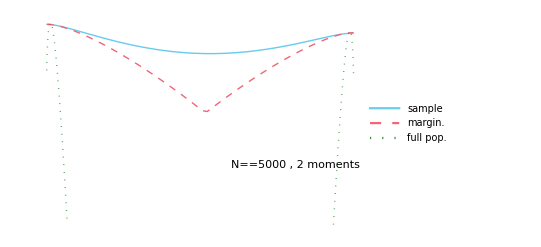

```mathematica
lplot=ListLogPlot[T/@{{ran/ni,qsamp*ni},{ran/ni,qmarg*ni},{rann/nn,qpop*nn}},Joined->True, PlotRange->{All,{10^-100,All}},PlotLegends->Placed[{"sample","margin.","full pop."},{0.8,0.15}],Epilog->Text[Style["N",Italic]==nn", 2 moments",Scaled[{0.8,0.3}]],FrameLabel->{OverBar[s],"prob. density"},ImageSize->a4shortside]
```

```mathematica
Export["logplot_5000.pdf",Style[lplot,Magnification->1],ImageResolution->300]
```

logplot_5000.pdf

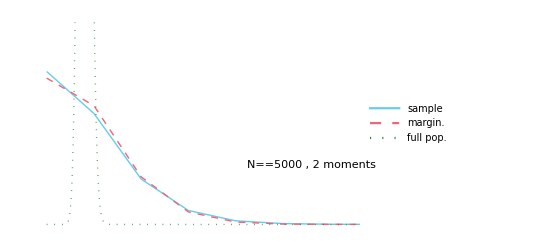

```mathematica
plot=ListPlot[T/@{{ran/ni,qsamp*ni},{ran/ni,qmarg*ni},{rann/nn,qpop*nn}},Joined->True, PlotRange->{{All,0.1},{All,40}},PlotLegends->Placed[{"sample","margin.","full pop."},{0.85,0.15}],Epilog->Text[Style["N",Italic]==nn ", 2 moments",Scaled[{0.85,0.3}]],FrameLabel->{OverBar[s],"prob. density"},ImageSize->a4shortside]
```

```mathematica
Export["plot_5000.pdf",Style[plot,Magnification->1],ImageResolution->300]
```

plot_5000.pdf

```mathematica
(* Using four moments *)
```

```mathematica
<<"ME_4momsolution3.m";<<"ME_4momsolution2.m";<<"ME_4momsolution.m";
```

```mathematica
(* load first four raw moments from Stensola data (3 ms) *)
n=65;means=Flatten@Import["norm_binomeans.csv"][[2;;]]
```

{0.0124204,0.000216286,4.59777×10^-6,1.07013×10^-7}

```mathematica
{aa1,aa2,aa3,aa4}=means;
```

```mathematica
nn=5000;rann=Range[0,nn];
```

```mathematica
(* find Lagr multipliers, four constraints. *)
{j1,j2,j3,j4,qpop,norm2}=MEhom4moments[aa1,aa2,aa3,aa4,nn,12];
```

```mathematica
{j1,j2,j3,j4}
```

{-29559.0871554,380136.767818,-4.15117643562×10^6,-327746.608152}

```mathematica
(* find Lagr multipliers, 2 constraints *)
{mj1,mj2,mjqq2ex,norm2}=MEhomsolution2[aa1,aa2,nn,12];
```

```mathematica
{zj1,zj2}
```

{-22449.2940092,22429.6391226}

```mathematica
Total[(qq2ex-pdf[5000])^2]
```

0.

```mathematica
(* compare higher moments *)
{{"measured",aa1,aa2,aa3,aa4},Prepend["predicted"]@Table[(Binomial[rann,i].qpop)/Binomial[nn,i],{i,4}]}//T//MF//N
```

(measured | predicted
0.0124204 | 0.0124195
0.000216286 | 0.000216274
4.59777×10^-6 | 4.59759×10^-6
1.07013×10^-7 | 1.07426×10^-7)

```mathematica
(* marginalize to subnetwork of 65 units*)
ni=n;ran=Range[0,ni];qmarg=Block[{list=ParallelTable[Table[condp2[ni,r,nn,rr],{rr,0,nn}].qpop,{r,0,ni},Method->"CoarsestGrained"]},list/Total[list]];
```

```mathematica
Total[(qqmarex-qqmarg[5000])^2]
```

3.40602×10^-33

```mathematica
(* compare higher moments *)
{{aa1,aa2,aa3,aa4},Table[(Binomial[ran,i].qmarg)/Binomial[ni,i],{i,4}]}//T//MF//N
```

(0.0124204 | 0.0124197
0.000216286 | 0.000215596
4.59777×10^-6 | 0.0000637286
1.07013×10^-7 | 0.0000610869)

```mathematica
(* maxent directly at subpopulation level *)

ni=n;ran=Range[0,ni];{sj1,sj2,sj3,sj4,qsamp,norm2x}=MEhom4moments[aa1,aa2,aa3,aa4,ni,12];
```

```mathematica
{sj1,sj2,sj3,sj4}
```

{-303.94775039,767.400115221,-3742.75849281,1093.36996577}

```mathematica
qqxs=MEhomprob[zj1x,zj2x,ni];
```

```mathematica
ni=2000;ran=Range[0,ni];{zj1x,zj2x,qqxt,norm2x}=MEhomsolution[aa1,aa2,ni,12];
```

```mathematica
{zj1x,zj2x}
```

{-6626.85811617,6618.01721347}

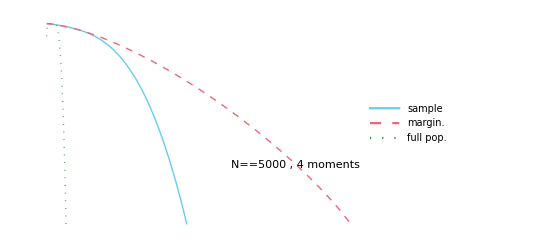

```mathematica
lplot=ListLogPlot[T/@{{ran/ni,qsamp*ni},{ran/ni,qmarg*ni},{rann/nn,qpop*nn}},Joined->True, PlotRange->{All,{10^-100,All}},PlotLegends->Placed[{"sample","margin.","full pop."},{0.8,0.15}],Epilog->Text[Style["N",Italic]==nn", 4 moments",Scaled[{0.8,0.3}]],FrameLabel->{OverBar[s],"prob. density"},ImageSize->a4shortside]
```

```mathematica
Export["logplot4mom_5000.pdf",Style[lplot,Magnification->1],ImageResolution->300]
```

logplot4mom_5000.pdf

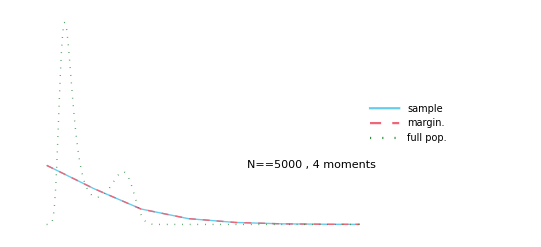

```mathematica
plot=ListPlot[T/@{{ran/ni,qsamp*ni},{ran/ni,qmarg*ni},{rann/nn,qpop*nn}},Joined->True, PlotRange->{{All,0.1},{All,All}},PlotLegends->Placed[{"sample","margin.","full pop."},{0.85,0.15}],Epilog->Text[Style["N",Italic]==nn ", 4 moments",Scaled[{0.85,0.3}]],FrameLabel->{OverBar[s],"prob. density"},ImageSize->a4shortside]
```

```mathematica
Export["plot4mom_5000.pdf",Style[plot,Magnification->1],ImageResolution->300]
```

plot4mom_5000.pdf

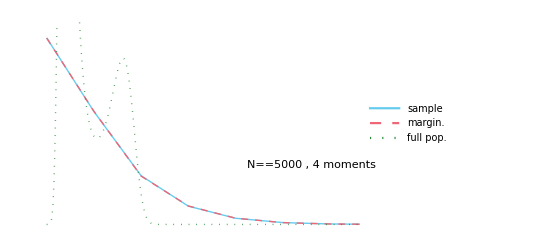

```mathematica
plot=ListPlot[T/@{{ran/ni,qsamp*ni},{ran/ni,qmarg*ni},{rann/nn,qpop*nn}},Joined->True, PlotRange->{{All,0.1},{All,35}},PlotLegends->Placed[{"sample","margin.","full pop."},{0.85,0.15}],Epilog->Text[Style["N",Italic]==nn ", 4 moments",Scaled[{0.85,0.3}]],FrameLabel->{OverBar[s],"prob. density"},ImageSize->a4shortside]
```

```mathematica
(* Numerical tests *)
```

```mathematica
{aa1,aa2}
```

{0.0124204,0.000216286}

```mathematica
{zj1,zj2}
```

{-22460.8632984,22450.9645408}

```mathematica
fe[js1_,js2_]:=Sum[Exp[Log[Binomial[nn,m]]+js1*(m/nn-aa1)+js2*((m^2-m)/(nn^2-nn)-aa2)],{m,0,nn}];
```

```mathematica
fm[js1_,js2_]:=NIntegrate[Exp[Log[Binomial[nn,m]]+js1*(m/nn-aa1)+js2*((m^2-m)/(nn^2-nn)-aa2)],{m,0,nn}];
```

```mathematica
Through[{fe,fm}[0,0]]
```

{1.41246703213938×10^1505,1.41246703214604×10^1505}

```mathematica
Through[{fe,fm}[zj1,zj2]]
```

{3.60794×10^144,3.60771×10^144}

```mathematica
Log[%]
```

{332.855,332.855}

```mathematica
MEhomsolutiont[meanmm_,meancorr_,nn_,wp_:MachinePrecision]:=Block[{totcorr=meancorr,totmm=meanmm,totalprob,zzzm,js2,js1,freeenm,varm,soluzm,prob,ran=Range[0,nn],bvalues},freeenm=Log@Sum[Binomial[nn,m]*Exp[js2*((m^2-m)/(nn^2-nn)-totcorr)+js1*(m/nn-totmm)],{m,0,nn}];
soluzm=NMinimize[freeenm,{js1,js2},MaxIterations->10000,PrecisionGoal->3,Method->Automatic,AccuracyGoal->Infinity,WorkingPrecision->wp];
prob=Table[Binomial[nn,m]*Exp[js2*(m^2-m)/(nn^2-nn)+js1*m/nn]/2^nn/.soluzm[[2]],{m,0,nn}];
totalprob=Total[prob];prob=prob/totalprob;
bvalues={(ran.prob/nn)/meanmm-1,((ran^2-ran).prob/(nn^2-nn))/meancorr-1};
Print["rel. discrepancies %: ",bvalues*100//N];
{js1/.soluzm[[2]],js2/.soluzm[[2]],prob,totalprob}]
```

```mathematica
AbsoluteTiming[{xj1,xj2,xqpop,xnorm}=MEhomsolution[aa1,aa2,7000,12];]
```

{58.7641,Null}

```mathematica
{xj1,xj2}
```

{-31445.1282644,31435.2393439}

```mathematica
AbsoluteTiming[{xj1,xj2,xqpop,xnorm}=MEhomsolutiont[aa1,aa2,7000,12];]
```

{52.9107,Null}

```mathematica
ni=n;ran=Range[0,ni];Do[solution=MEhomsolutiont[aa1,aa2,kk,12];

qmarg=Block[{list=ParallelTable[Table[condp2[ni,r,kk,rr],{rr,0,kk}].(solution[[3]]),{r,0,ni},Method->"CoarsestGrained"]},list/Total[list]];

Save["stensola2mom_"<>ToString[kk]<>".m",{solution,qmarg}];,{kk,9000,10000,1000}]
```

```mathematica
<<"ME_4momsolution.m";
```

```mathematica
AbsoluteTiming[solu=MEhom4moments[aa1,aa2,aa3,aa4,5000,12];]
```

{156.116,Null}

```mathematica
ni=n;ran=Range[0,ni];Do[solution=MEhom4moments[aa1,aa2,aa3,aa4,kk,12];

qmarg=Block[{list=ParallelTable[Table[condp2[ni,r,kk,rr],{rr,0,kk}].(solution[[5]]),{r,0,ni},Method->"CoarsestGrained"]},list/Total[list]];

Save["_stensola4mom_"<>ToString[kk]<>".m",{solution,qmarg}];,{kk,9000,10000,1000}]
```

```mathematica
{xj1,xj2}
```

{-31445.1365361,31435.2398333}

```mathematica
AbsoluteTiming[{xj1,xj2,xqpop,xnorm}=MEhomsolutiont[aa1,aa2,7000,12];]
```

{41.4137,Null}

```mathematica
{xj1,xj2}
```

{-31445.1357911,31435.2417204}

```mathematica
AbsoluteTiming[{xj1,xj2,xqpop,xnorm}=MEhomsolutiont[aa1,aa2,10000,12];]
```

{61.5207,Null}

```mathematica
{xj1,xj2}
```

{-44921.5380445,44911.6307106}

```mathematica
freeenm[js1_,js2_,nn_]:=NIntegrate[Binomial[nn,m]*Exp[js2*((m^2-m)/(nn^2-nn)-aa2)+js1*(m/nn-aa1)],{m,0,nn}]
```

```mathematica
freeenm[0.918621214872,0.716688753379]
```

2.64407916737641×10^1505

```mathematica
NMinimize[freeenm[js1,js2,100],{js1,js2},MaxIterations->10000,PrecisionGoal->6,Method->Automatic,AccuracyGoal->Infinity,WorkingPrecision->12]
```

$Aborted

```mathematica
ClearAll[nn,j1,j2,rann];nn=5000;j2=5.696/nn;j1=-nn*j2*28/100-Log[nn*j2]*72/100;(*j1=-2550/nn;*)rann=(Range[0,nn]/nn);{j1,j2,l1=j1*nn,l2=j2*nn*(nn-1)/2}//N
```

{-2.84751,0.0011392,-14237.6,14237.2}

```mathematica
Clear[qq];qq=Block[{list=Table[mep[rr,nn,l1,l2],{rr,0,nn}]//N},list/Total[list]];
```

```mathematica
{a1=Table[rr/nn,{rr,0,nn}].qq//N,a2=Table[rr*(rr-1)/(nn*(nn-1)),{rr,0,nn}].qq//N}
```

$Aborted[]

```mathematica
ListPlot[T@{rann,qq*nn}, Joined->True,PlotRange->All]
```

```mathematica
ListLogPlot[T@{rann,qq*nn}, Joined->True]
```

```mathematica
ni=200;qqmar=Block[{list=Table[condp[ni,r,nn,rr],{r,0,ni},{rr,0,nn}].(qq//N)},list/Total[list]];
```

```mathematica
ni=200;ran=(Range[0,ni]/ni);ListLogPlot[{T@{ran,qqmar*ni},T@{rann,qq*nn}}, Joined->True]
```

```mathematica
ListPlot[{T@{ran,qqmar*ni},T@{rann,qq*nn}}, Joined->True,PlotRange->All]
```

```mathematica
<<"scripts/ME_homsolution.m"
```

```mathematica
a1=Table[rr/nn,{rr,0,nn}].qq//N
```

0.432501

```mathematica
a2=Table[rr*(rr-1)/(nn*(nn-1)),{rr,0,nn}].qq//N
```

0.353175

```mathematica
{zj1,zj2,qqx}=MEhomsolution[a1,a2,ni,30][[1;;3]];
```

```mathematica
ListLogPlot[{T@{ran,qqx*ni},T@{ran,qqmar*ni}}, Joined->True,PlotStyle->{{blue,Dashed,Thick},red}]
```

```mathematica
ListPlot[{T@{ran,qqx*ni},T@{ran,qqmar*ni}}, Joined->True,PlotStyle->{{blue,Dashed,Thick},red},PlotRange->All]
```